```mathematica
spring1 = Import["~/Downloads/spring1.csv", "CSV", "HeaderLines"->1];
spring2 = Import["~/Downloads/spring2.csv", "CSV", "HeaderLines"->1];
spring3 = Import["~/Downloads/spring3.csv", "CSV", "HeaderLines"->1];
spring4 = Import["~/Downloads/spring4.csv", "CSV", "HeaderLines"->1];
spring5 = Import["~/Downloads/spring5.csv", "CSV", "HeaderLines"->1];
spring6 = Import["~/Downloads/spring6.csv", "CSV", "HeaderLines"->1];
```

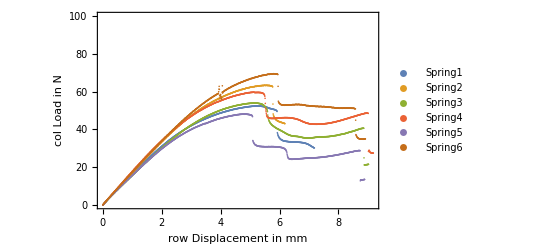

```mathematica
ListPlot[{spring1[[All, {2,3}]], spring2[[All, {2,3}]], spring3[[All, {2,3}]], spring4[[All, {2,3}]], spring5[[All, {2,3}]], spring6[[All, {2,3}]]}, Frame->True,PlotRange->{0,100},FrameLabel->{"row Displacement in mm","col Load in N"}, PlotLegends->{"Spring1","Spring2", "Spring3", "Spring4", "Spring5", "Spring6"}]
```